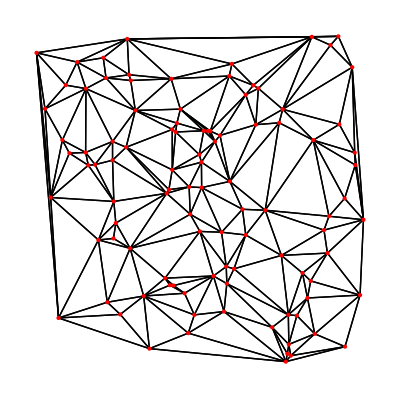

```mathematica
SeedRandom[1];
bboxL=1;
bboxH=1;
Nnodes=100;
p0=Table[0,{i,Nnodes},{i,2}];
Do[p0[[i,1]]=RandomReal[{0,bboxL}];
p0[[i,2]]=RandomReal[{0,bboxH}];,{i,Nnodes}];

timeStep=0.2;

Needs["ComputationalGeometry`"];
dt=DelaunayTriangulation[p0];
toPairs[{m_,ns_List}]:=Map[{m,#}&,ns];
edges=Flatten[Map[toPairs,dt],1];
Graphics[GraphicsComplex[p0,{Line[edges],Red,PointSize[Medium],Point[p0]}]]
```